```mathematica
Needs["EDA`"]
```

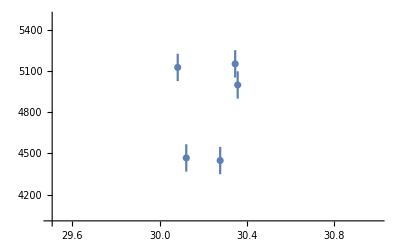

```mathematica
mydata={{{30.08351718,0.01},{5128,100}},{{30.12281397,0.01},{4467,100}},{{30.27830386,0.01},{4448,100}},{{30.34715207,0.01},{5154,100}},{{30.35860257,0.01},{5000,100}}};
EDAListPlot[mydata,PlotRange->{{29.5,31},{4000,5500}}]
mydata2={{30.08351718,5128},{30.12281397,4467},{30.27830386,4448},{30.34715207,5154},{30.35860257,5000}};
```

```mathematica
methods={Automatic,{"NMinimize",Method->"NelderMead"},{"NMinimize",Method->"DifferentialEvolution"},{"NMinimize",Method->"SimulatedAnnealing"},{"NMinimize",Method->"RandomSearch"}};
nlm100=NonlinearModelFit[mydata2,{aa Cos[ff xx + p]+bb,{aa>1000,ff<-3,ff>-12,p>0,p<Pi,bb>1000}},{aa,ff,p,bb},{xx},ConfidenceLevel->.9 ,Method->#]&/@methods;
TableForm[Transpose@{nlm100},TableAlignments->Left]
nlm100[[1]][{"ParameterConfidenceIntervalTable"}];
nlm100[[2]][{"ParameterConfidenceIntervalTable"}];
nlm100[[3]][{"ParameterConfidenceIntervalTable"}];
nlm100[[4]][{"ParameterConfidenceIntervalTable"}];
nlm100[[5]][{"ParameterConfidenceIntervalTable"}];
```

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {7.77703×10^-7, 0.0000300622, 1.39021×10^-7}, is returned.

FittedModel[5152.27+1002.05 Cos[0.138351-10.9222 xx]]
FittedModel[18299.2+13709.7 Cos[0.-3.01448 xx]]
FittedModel[3909.86+1000. Cos[2.90936-3. xx]]
FittedModel[1000.+5719.56 Cos[3.14159-3. xx]]
FittedModel[6547.27+2356.51 Cos[0.325923-6.56111 xx]]

FittedModel::constr: The property values {"ParameterConfidenceIntervalTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

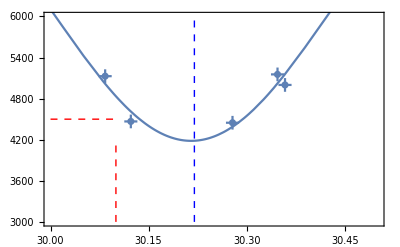

```mathematica
lineStyle={Thin,Red,Dashed};
line11=Line[{{30.0,4500},{30.1,4500}}];
line12=Line[{{30.1,3000},{30.1,4183.648763648759}}];
lineStyle2={Thin,Blue,Dashed};
line2=Line[{{30.22,3000},{30.22,6000}}];
Show[EDAListPlot[mydata,PlotRange->{{30.0,30.5},{3000,6000}}],Plot[5955.348898589061+1771.7001349403015 Cos[3.1235941364458886-7.693489520741468 xx],{xx,29.5,31}],Frame->True,Epilog->{{Directive[lineStyle],line11,line12},{Directive[lineStyle2],line2}}]
```

```mathematica
5955.348898589061-1771.7001349403015
```

4183.65